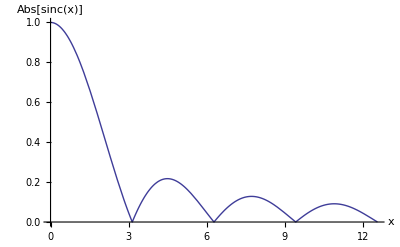

```mathematica
Plot[
Abs[Sinc[x]], {x, 0, 4 Pi}
, AxesLabel->{x, Abs[Sinc[x]]}
, PlotRange->Full
]

(* 
http://mathematica.stackexchange.com/questions/15929/how-to-make-the-file-size-for-mathematica-9-export-graphic-smaller-like-mathema *)

(*too big*)
(*Export["C:\\Users\\Peeter\\cygwin_home\\physicsplay\\notes\\blogit\\foo9.pdf", %]*)

(*okay*)
(*Export["C:\\Users\\Peeter\\cygwin_home\\physicsplay\\notes\\blogit\\foo9.pdf",First[ImportString[ExportString[%,"PDF"],"PDF"]]]*)
```